## Pixel window functions

### 2-d round pixel of radius R

```mathematica
W2[k_, R_]=(π R^2)^-1 Integrate[r  Exp[I k r Cos[ϕ]], {r,0,R},{ϕ,0,2π},Assumptions->{k>0, R>0}]
```

(2 BesselJ[1,k R])/(k R)

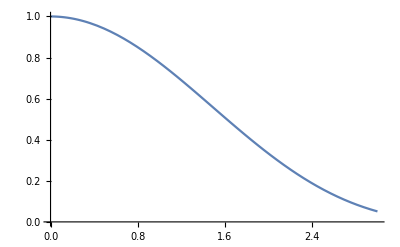

```mathematica
Plot[W2[kR,1]^2, {kR,0,3},PlotRange->{0,1}]
```

### square pixel of side λ (symmetrized)

```mathematica
Wsquare[k_,λ_]:=W2[k,λ/√π]
```

#### check limits

```mathematica
Limit[Wsquare[k,λ], k->0]
```

1

but it only works in the limit…

```mathematica
Wsquare[0,1]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 √π ComplexInfinity encountered.

Indeterminate

#### numerical checks for our case

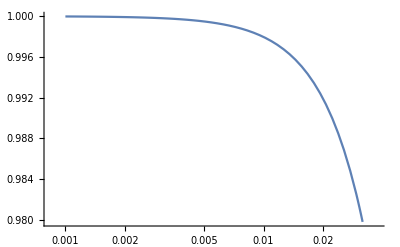

```mathematica
LogLinearPlot[Wsquare[k, 2048/128]^2, {k,10^-3,10^-1.5},PlotRange->All]
```

```mathematica
Wsquare[10^-1.5,2048/128]^2
```

0.9798

### square pixel of side λ (2D)

```mathematica
Wsquare1D[k_,λ_]:= SphericalBesselJ[0,k λ/2]
WSquare2D[kx_, ky_, λ_]:=SphericalBesselJ[0,kx λ/2]SphericalBesselJ[0,ky λ/2]
```

```mathematica
Integrate[WSquare2D[k Cos[ϕ], k Sin[ϕ],1] k, {ϕ,0,2π},Assumptions->k>0]
```

Integrate[k SphericalBesselJ[0,1/2 k Cos[ϕ]] SphericalBesselJ[0,1/2 k Sin[ϕ]],{ϕ,0,2 π},Assumptions→k>0]

#### check limits

```mathematica
Limit[Wsquare[k,λ], k->0]
```

1

but it only works in the limit…

```mathematica
Wsquare[0,1]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 √π ComplexInfinity encountered.

Indeterminate

#### numerical checks for our case

```mathematica
LogLinearPlot[Wsquare[k, 2048/128]^2, {k,10^-3,10^-1.5},PlotRange->All]
```

-Graphics-

```mathematica
Wsquare[10^-1.5,2048/128]^2
```

0.9798

### 1-d round pixel of size L

```mathematica
W1[k_, L_]=(L)^-1 Integrate[  Exp[I k r ], {r,-L/2,L/2},Assumptions->{k>0, L>0}]
```

(2 Sin[(k L)/2])/(k L)

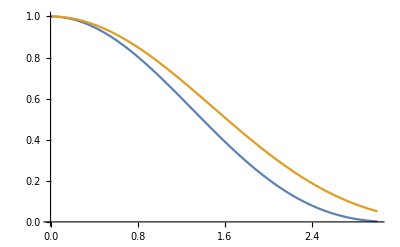

```mathematica
Plot[{W1[2kR,1]^2,W2[kR,1]^2}, {kR,0,3},PlotRange->{0,1}]
```

should really do azimuthal average of the square-pixel window

```mathematica
Wazim[k_, L_]=Integrate[ Exp[ⅈ k √(x^2+y^2) Cos[ArcTan[x,y]]], {x,y}∈Rectangle[{-L/2,-L/2}, {L/2,L/2}],Assumptions->{k≥0,L>0}]/L^2
```

(2 Sin[(k L)/2])/(k L)

```mathematica
Limit[Wazim[k,l,ψ],ψ->π/3]
```

(16 Sin[(k l)/4] Sin[1/4 √3 k l])/(√3 k^2 l^2)

```mathematica
FullSimplify[(4 Csc[ψ] Sec[ψ] Sin[1/2 k L Cos[ψ]] Sin[1/2 k L Sin[ψ]])/(k^2 L^2)]
```

(4 Csc[ψ] Sec[ψ] Sin[1/2 k L Cos[ψ]] Sin[1/2 k L Sin[ψ]])/(k^2 L^2)

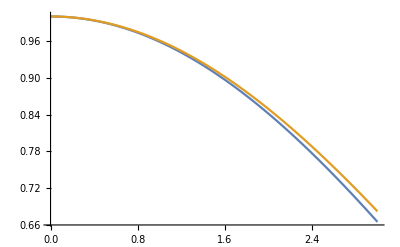

```mathematica
Plot[{Wazim[k,1], Wsquare[k,1]}, {k,0,3}]
```

```mathematica
Limit[Wazim[k,l], k->0]
```

1

```mathematica
√(x^2+y^2) Cos[ArcTan[x,y]]//FullSimplify
```

x

```mathematica
Integrate[ Exp[ⅈ (kx x + ky y)], {x,-L/2,L/2}, {y,-L/2,L/2},Assumptions->{kx≥0,ky≥0,L>0}]/L^2
```

(4 Sin[(kx L)/2] Sin[(ky L)/2])/(kx ky L^2)

```mathematica
%2/.ky->Sqrt[k^2-kx^2]//FullSimplify[#, Assumptions->{kx≥0,ky≥0,L>0}]&
```

(4 Sin[(kx L)/2] Sin[1/2 √(k^2-kx^2) L])/(kx √((k-kx) (k+kx)) L^2)

```mathematica
Limit[%2, ky->0]
```

(2 Sin[(kx L)/2])/(kx L)

```mathematica
%2==SphericalBesselJ[0,L Sqrt[kx^2+ky^2]/2]//FullSimplify
```

(4 Sin[(kx L)/2] Sin[(ky L)/2])/(kx ky L^2)==Sinc[1/2 √(kx^2+ky^2) L]

```mathematica
%15/.{L->1, kx->2,ky->3}
```

False

```mathematica
Integrate[(4 Csc[ψ] Sec[ψ] Sin[1/2 k L Cos[ψ]] Sin[1/2 k L Sin[ψ]])/(k^2 L^2), {ψ,0,2π},Assumptions->{k≥0,L>0}]/(2π)
```

Integrate[(4 Csc[ψ] Sec[ψ] Sin[1/2 k L Cos[ψ]] Sin[1/2 k L Sin[ψ]])/(k^2 L^2),{ψ,0,2 π},Assumptions→{k≥0,L>0}]/(2 π)

### 1D pixel

```mathematica
W1[k_, R_]=(L)^-1 Integrate[Exp[I k r], {r,-L/2,L/2},Assumptions->{k>0, L>0}]
```

(2 Sin[(k L)/2])/(k L)

### Sampling

So far, we’ve left out one important part: the final map only has one pixel per “window”, rather than the original number. This is like multiplying by a DiracComb in real space, or convolving with the comb in Fourier space (which is a complicated operation)...